```mathematica
dir="C:\\Users\\mfroelin\\Desktop\\ScientificColourMaps8"
```

C:\Users\mfroelin\Desktop\ScientificColourMaps8

```mathematica
colNames=FileBaseName/@Select[Select[FileNames["*",dir],DirectoryQ],StringTake[FileBaseName@#,1]=!="+"&];
cols=({#,a=FileBaseName/@Select[FileNames["*",FileNameJoin[{dir,#}]],DirectoryQ]})&/@colNames;
```

```mathematica
grads=Select[cols,StringTake[#[[1]],-1]=!="O"&&Length[#[[2]]]===2&];
grads2=Select[cols,StringTake[#[[1]],-1]=!="O"&&Length[#[[2]]]===1&];
cyclic=Select[cols,StringTake[#[[1]],-1]==="O"&];
```

```mathematica
{
1->{"Name","StandardName","Discription","AlernateName"},
2->{"Group"..},
3->1,
4->"Named or Range; {names..}; {1,∞,1},{1,9,1}; {0,1}...",
5->"ColorList or ColorFunction",
6->"Named->AlternateNames; Indexed->{Indexed, AltName}; physical->explenation",
7->"Named->hueorder else nothing",
8->"Named->explenation"
}
```

```mathematica
AddScientificColours[dir_]:=Block[{grads,gradDiv,gradMulti,cyclic,all,swatches,colName,groupName,getCol,colRange,allDef,
nameDef,groupDef,newGroupsPattern,newShemeNames,newShemes},

(*activated ColorDataDump*)
ColorData[];

(*color functions defined in scientific colour maps v8*)
grads={"acton","bamako","batlow","batlowK","batlowW","bilbao","buda","davos","devon","glasgow","grayC","hawaii","imola","lajolla","lapaz","lipari","navia","nuuk","oslo","tokyo","turku"};
gradDiv={"bam","berlin","broc","cork","lisbon","managua","roma","tofino","vanimo","vik"};
gradMulti={"fes","bukavu","oleron"};
cyclic={"bamO","brocO","corkO","romaO","vikO"};

all=Join[grads,gradDiv,gradMulti,cyclic];

(*number of swatches for each*)
swatches={"10",(*"25",*)"50"(*,"100"*)};

(*functions that generate the information needed for the named colorfunctions*)
colName=Switch[#2,
1,{Capitalize[#1],#1,{}},
2,{Capitalize[#1]<>"Discrete",#1<>" discrete",{}},
3,{Capitalize[#1]<>"Categorical"<>#3,#1<>" categorical "<>#3,{}}
]&;
groupName={
If[#2===1,"Gradients","Indexed"],
"ScientificColorMaps",
Which[
MemberQ[grads,#1],"Sequential",
MemberQ[gradDiv,#1],"Diverging",
MemberQ[gradMulti,#1],"MultiSequential",
MemberQ[cyclic,#1],"Cyclic"
]<>"Gradients"<>Switch[#2,1,"",2,"Discrete",3,"Categorical"]
}&;
getCol=Switch[#2,
1,
If[!MemberQ[gradMulti,#1],
RGBColor/@Import[FileNameJoin[{dir,#1,#1}]<>".txt","Data"],
Transpose@{Join[Subdivide[0.,0.5,127],Subdivide[0.5,1.,127]],
RGBColor/@Import[FileNameJoin[{dir,#1,#1}]<>".txt","Data"]}
]
,
2,RGBColor/@Import[FileNameJoin[{dir,#1,"CategoricalPalettes",#1}]<>"S.txt","Data"],
3,RGBColor[ToExpression@StringSplit[#][[1;;3]]/255]&/@Import[FileNameJoin[{dir,#1,"DiscretePalettes",#1}]<>#3<>".txt","Lines"][[3;;]]
]&;
colRange=Switch[#1,
1,{0,1},
2,{1,100,1},
3,{1,ToExpression[#2],1}]&;

(*generate all color functions*)
allDef=Flatten[Table[
{colName[name,i,j],groupName[name,i,j],1,colRange[i,j],getCol[name,i,j],""}
,{name,all},{i,If[MemberQ[grads,name],{1,2,3},{1,3}]},{j,If[i==3,swatches,{""}]}],2];

nameDef=allDef[[All,1,1]];
groupDef=DeleteCases[DeleteCases[DeleteDuplicates[Flatten[allDef[[All,2]]]],"Gradients"],"Indexed"];
newGroupsPattern=Alternatives@@Join[DataPaclets`ColorDataDump`colorSchemeGroupsPattern/.Alternatives->List,groupDef];
newShemeNames=Join[DataPaclets`ColorDataDump`colorSchemeNames,nameDef];
newShemes=Join[DataPaclets`ColorDataDump`colorSchemes,allDef];

DataPaclets`ColorDataDump`colorSchemeGroupsPattern=newGroupsPattern;
DataPaclets`ColorDataDump`colorSchemeNames=newShemeNames;
DataPaclets`ColorDataDump`colorSchemes=newShemes;
]
```

```mathematica
AddScientificColours@"C:\\Users\\mfroelin\\Desktop\\ScientificColourMaps8"
```

{AlternateNames,ColorFunction,ColorList,ColorRules,Image,Name,Panel,ParameterCount,Range,StandardName}

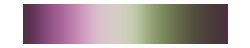
{{},ColorDataFunction[…],Missing[NotApplicable],Missing[NotApplicable],-Graphics-,bamO,-Graphics-,1,{0,1},BamO}

```mathematica
ColorData["BamO",#]&/@ColorData["Properties"]
```

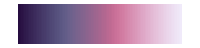
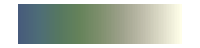
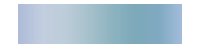
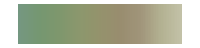
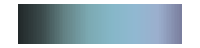
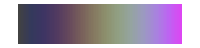
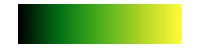
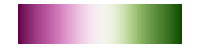
Acton
-Graphics- | AlpineColors
-Graphics- | Aquamarine
-Graphics- | ArmyColors
-Graphics- | AtlanticColors
-Graphics- | AuroraColors
-Graphics-
AvocadoColors
-Graphics- | Bam
-Graphics- | Bamako
-Graphics- | BamO
-Graphics- | Batlow
-Graphics- | BatlowK
-Graphics-
BatlowW
-Graphics- | BeachColors
-Graphics- | Berlin
-Graphics- | Bilbao
-Graphics- | BlueGreenYellow
-Graphics- | BrassTones
-Graphics-
BrightBands
-Graphics- | Broc
-Graphics- | BrocO
-Graphics- | BrownCyanTones
-Graphics- | Buda
-Graphics- | Bukavu
-Graphics-
CandyColors
-Graphics- | CherryTones
-Graphics- | CMYKColors
-Graphics- | CoffeeTones
-Graphics- | Cork
-Graphics- | CorkO
-Graphics-
DarkBands
-Graphics- | DarkRainbow
-Graphics- | DarkTerrain
-Graphics- | Davos
-Graphics- | DeepSeaColors
-Graphics- | Devon
-Graphics-
FallColors
-Graphics- | Fes
-Graphics- | FruitPunchColors
-Graphics- | FuchsiaTones
-Graphics- | Glasgow
-Graphics- | GrayC
-Graphics-
GrayTones
-Graphics- | GrayYellowTones
-Graphics- | GreenBrownTerrain
-Graphics- | GreenPinkTones
-Graphics- | Hawaii
-Graphics- | Imola
-Graphics-
IslandColors
-Graphics- | Lajolla
-Graphics- | LakeColors
-Graphics- | Lapaz
-Graphics- | LightTemperatureMap
-Graphics- | LightTerrain
-Graphics-
Lipari
-Graphics- | Lisbon
-Graphics- | Managua
-Graphics- | MintColors
-Graphics- | Navia
-Graphics- | NeonColors
-Graphics-
Nuuk
-Graphics- | Oleron
-Graphics- | Oslo
-Graphics- | Pastel
-Graphics- | PearlColors
-Graphics- | PigeonTones
-Graphics-
PlumColors
-Graphics- | Rainbow
-Graphics- | RedBlueTones
-Graphics- | RedGreenSplit
-Graphics- | Roma
-Graphics- | RomaO
-Graphics-
RoseColors
-Graphics- | RustTones
-Graphics- | SandyTerrain
-Graphics- | SiennaTones
-Graphics- | SolarColors
-Graphics- | SouthwestColors
-Graphics-
StarryNightColors
-Graphics- | SunsetColors
-Graphics- | TemperatureMap
-Graphics- | ThermometerColors
-Graphics- | Tofino
-Graphics- | Tokyo
-Graphics-
Turku
-Graphics- | ValentineTones
-Graphics- | Vanimo
-Graphics- | Vik
-Graphics- | VikO
-Graphics- | WatermelonColors
-Graphics-

```mathematica
Grid[Partition[Column[{#,Show[ColorData[#,"Image"],ImageSize->200]},Alignment->Center]&/@ColorData["Gradients"],6,6,1,{}],Spacings->.5,Frame->All]
```

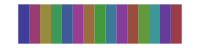
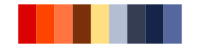
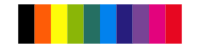
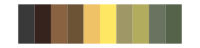
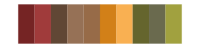
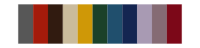
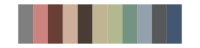
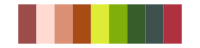
1
-Graphics- | 2
-Graphics- | 3
-Graphics- | 4
-Graphics- | 5
-Graphics- | 6
-Graphics-
7
-Graphics- | 8
-Graphics- | 9
-Graphics- | 10
-Graphics- | 11
-Graphics- | 12
-Graphics-
13
-Graphics- | 14
-Graphics- | 15
-Graphics- | 16
-Graphics- | 17
-Graphics- | 18
-Graphics-
19
-Graphics- | 20
-Graphics- | 21
-Graphics- | 22
-Graphics- | 23
-Graphics- | 24
-Graphics-
25
-Graphics- | 26
-Graphics- | 27
-Graphics- | 28
-Graphics- | 29
-Graphics- | 30
-Graphics-
31
-Graphics- | 32
-Graphics- | 33
-Graphics- | 34
-Graphics- | 35
-Graphics- | 36
-Graphics-
37
-Graphics- | 38
-Graphics- | 39
-Graphics- | 40
-Graphics- | 41
-Graphics- | 42
-Graphics-
43
-Graphics- | 44
-Graphics- | 45
-Graphics- | 46
-Graphics- | 47
-Graphics- | 48
-Graphics-
49
-Graphics- | 50
-Graphics- | 51
-Graphics- | 52
-Graphics- | 53
-Graphics- | 54
-Graphics-
55
-Graphics- | 56
-Graphics- | 57
-Graphics- | 58
-Graphics- | 59
-Graphics- | 60
-Graphics-
61
-Graphics- | 62
-Graphics- | 63
-Graphics- | 64
-Graphics- | 65
-Graphics- | 66
-Graphics-
67
-Graphics- | 68
-Graphics- | 69
-Graphics- | 70
-Graphics- | 71
-Graphics- | 72
-Graphics-
73
-Graphics- | 74
-Graphics- | 75
-Graphics- | 76
-Graphics- | 77
-Graphics- | 78
-Graphics-
79
-Graphics- | 80
-Graphics- | 81
-Graphics- | 82
-Graphics- | 83
-Graphics- | 84
-Graphics-
85
-Graphics- | 86
-Graphics- | 87
-Graphics- | 88
-Graphics- | 89
-Graphics- | 90
-Graphics-
91
-Graphics- | 92
-Graphics- | 93
-Graphics- | 94
-Graphics- | 95
-Graphics- | 96
-Graphics-
97
-Graphics- | 98
-Graphics- | 99
-Graphics- | 100
-Graphics- | 101
-Graphics- | 102
-Graphics-
103
-Graphics- | 104
-Graphics- | 105
-Graphics- | 106
-Graphics- | 107
-Graphics- | 108
-Graphics-
109
-Graphics- | 110
-Graphics- | 111
-Graphics- | 112
-Graphics- | 113
-Graphics- | 114
-Graphics-
115
-Graphics- | ActonCategorical10
-Graphics- | ActonCategorical100
-Graphics- | ActonCategorical25
-Graphics- | ActonCategorical50
-Graphics- | ActonDiscrete
-Graphics-
BamakoCategorical10
-Graphics- | BamakoCategorical100
-Graphics- | BamakoCategorical25
-Graphics- | BamakoCategorical50
-Graphics- | BamakoDiscrete
-Graphics- | BamCategorical10
-Graphics-
BamCategorical100
-Graphics- | BamCategorical25
-Graphics- | BamCategorical50
-Graphics- | BamOCategorical10
-Graphics- | BamOCategorical100
-Graphics- | BamOCategorical25
-Graphics-
BamOCategorical50
-Graphics- | BatlowCategorical10
-Graphics- | BatlowCategorical100
-Graphics- | BatlowCategorical25
-Graphics- | BatlowCategorical50
-Graphics- | BatlowDiscrete
-Graphics-
BatlowKCategorical10
-Graphics- | BatlowKCategorical100
-Graphics- | BatlowKCategorical25
-Graphics- | BatlowKCategorical50
-Graphics- | BatlowKDiscrete
-Graphics- | BatlowWCategorical10
-Graphics-
BatlowWCategorical100
-Graphics- | BatlowWCategorical25
-Graphics- | BatlowWCategorical50
-Graphics- | BatlowWDiscrete
-Graphics- | BerlinCategorical10
-Graphics- | BerlinCategorical100
-Graphics-
BerlinCategorical25
-Graphics- | BerlinCategorical50
-Graphics- | BilbaoCategorical10
-Graphics- | BilbaoCategorical100
-Graphics- | BilbaoCategorical25
-Graphics- | BilbaoCategorical50
-Graphics-
BilbaoDiscrete
-Graphics- | BrocCategorical10
-Graphics- | BrocCategorical100
-Graphics- | BrocCategorical25
-Graphics- | BrocCategorical50
-Graphics- | BrocOCategorical10
-Graphics-
BrocOCategorical100
-Graphics- | BrocOCategorical25
-Graphics- | BrocOCategorical50
-Graphics- | BudaCategorical10
-Graphics- | BudaCategorical100
-Graphics- | BudaCategorical25
-Graphics-
BudaCategorical50
-Graphics- | BudaDiscrete
-Graphics- | BukavuCategorical10
-Graphics- | BukavuCategorical100
-Graphics- | BukavuCategorical25
-Graphics- | BukavuCategorical50
-Graphics-
CorkCategorical10
-Graphics- | CorkCategorical100
-Graphics- | CorkCategorical25
-Graphics- | CorkCategorical50
-Graphics- | CorkOCategorical10
-Graphics- | CorkOCategorical100
-Graphics-
CorkOCategorical25
-Graphics- | CorkOCategorical50
-Graphics- | DavosCategorical10
-Graphics- | DavosCategorical100
-Graphics- | DavosCategorical25
-Graphics- | DavosCategorical50
-Graphics-
DavosDiscrete
-Graphics- | DevonCategorical10
-Graphics- | DevonCategorical100
-Graphics- | DevonCategorical25
-Graphics- | DevonCategorical50
-Graphics- | DevonDiscrete
-Graphics-
FesCategorical10
-Graphics- | FesCategorical100
-Graphics- | FesCategorical25
-Graphics- | FesCategorical50
-Graphics- | GlasgowCategorical10
-Graphics- | GlasgowCategorical100
-Graphics-
GlasgowCategorical25
-Graphics- | GlasgowCategorical50
-Graphics- | GlasgowDiscrete
-Graphics- | GrayCCategorical10
-Graphics- | GrayCCategorical100
-Graphics- | GrayCCategorical25
-Graphics-
GrayCCategorical50
-Graphics- | GrayCDiscrete
-Graphics- | HawaiiCategorical10
-Graphics- | HawaiiCategorical100
-Graphics- | HawaiiCategorical25
-Graphics- | HawaiiCategorical50
-Graphics-
HawaiiDiscrete
-Graphics- | ImolaCategorical10
-Graphics- | ImolaCategorical100
-Graphics- | ImolaCategorical25
-Graphics- | ImolaCategorical50
-Graphics- | ImolaDiscrete
-Graphics-
LajollaCategorical10
-Graphics- | LajollaCategorical100
-Graphics- | LajollaCategorical25
-Graphics- | LajollaCategorical50
-Graphics- | LajollaDiscrete
-Graphics- | LapazCategorical10
-Graphics-
LapazCategorical100
-Graphics- | LapazCategorical25
-Graphics- | LapazCategorical50
-Graphics- | LapazDiscrete
-Graphics- | LipariCategorical10
-Graphics- | LipariCategorical100
-Graphics-
LipariCategorical25
-Graphics- | LipariCategorical50
-Graphics- | LipariDiscrete
-Graphics- | LisbonCategorical10
-Graphics- | LisbonCategorical100
-Graphics- | LisbonCategorical25
-Graphics-
LisbonCategorical50
-Graphics- | ManaguaCategorical10
-Graphics- | ManaguaCategorical100
-Graphics- | ManaguaCategorical25
-Graphics- | ManaguaCategorical50
-Graphics- | NaviaCategorical10
-Graphics-
NaviaCategorical100
-Graphics- | NaviaCategorical25
-Graphics- | NaviaCategorical50
-Graphics- | NaviaDiscrete
-Graphics- | NuukCategorical10
-Graphics- | NuukCategorical100
-Graphics-
NuukCategorical25
-Graphics- | NuukCategorical50
-Graphics- | NuukDiscrete
-Graphics- | OleronCategorical10
-Graphics- | OleronCategorical100
-Graphics- | OleronCategorical25
-Graphics-
OleronCategorical50
-Graphics- | OsloCategorical10
-Graphics- | OsloCategorical100
-Graphics- | OsloCategorical25
-Graphics- | OsloCategorical50
-Graphics- | OsloDiscrete
-Graphics-
RomaCategorical10
-Graphics- | RomaCategorical100
-Graphics- | RomaCategorical25
-Graphics- | RomaCategorical50
-Graphics- | RomaOCategorical10
-Graphics- | RomaOCategorical100
-Graphics-
RomaOCategorical25
-Graphics- | RomaOCategorical50
-Graphics- | TofinoCategorical10
-Graphics- | TofinoCategorical100
-Graphics- | TofinoCategorical25
-Graphics- | TofinoCategorical50
-Graphics-
TokyoCategorical10
-Graphics- | TokyoCategorical100
-Graphics- | TokyoCategorical25
-Graphics- | TokyoCategorical50
-Graphics- | TokyoDiscrete
-Graphics- | TurkuCategorical10
-Graphics-
TurkuCategorical100
-Graphics- | TurkuCategorical25
-Graphics- | TurkuCategorical50
-Graphics- | TurkuDiscrete
-Graphics- | VanimoCategorical10
-Graphics- | VanimoCategorical100
-Graphics-
VanimoCategorical25
-Graphics- | VanimoCategorical50
-Graphics- | VikCategorical10
-Graphics- | VikCategorical100
-Graphics- | VikCategorical25
-Graphics- | VikCategorical50
-Graphics-
VikOCategorical10
-Graphics- | VikOCategorical100
-Graphics- | VikOCategorical25
-Graphics- | VikOCategorical50
-Graphics- |  |

```mathematica
Grid[Partition[Column[{#,Show[ColorData[#,"Image"],ImageSize->200]},Alignment->Center]&/@ColorData["Indexed"],6,6,1,{}],Spacings->.5,Frame->All]
```

```mathematica
newShemes[[-1]]
```

Part::partd: Part specification newShemes⟦-1⟧ is longer than depth of object.

newShemes⟦-1⟧

```mathematica
{"Atoms","Crayola","GeologicAges","HTML","Legacy","WebSafe",1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,"DarkRainbow","Rainbow","Pastel","Aquamarine","BrassTones","BrownCyanTones","CherryTones","CoffeeTones","FuchsiaTones","GrayTones","GrayYellowTones","GreenPinkTones","PigeonTones","RedBlueTones","RustTones","SiennaTones","ValentineTones","AlpineColors","ArmyColors","AtlanticColors","AuroraColors","AvocadoColors","BeachColors","CandyColors","CMYKColors","DeepSeaColors","FallColors","FruitPunchColors","IslandColors","LakeColors","MintColors","NeonColors","PearlColors","PlumColors","RoseColors","SolarColors","SouthwestColors","StarryNightColors","SunsetColors","ThermometerColors","WatermelonColors","RedGreenSplit","DarkTerrain","GreenBrownTerrain","LightTerrain","SandyTerrain","BlueGreenYellow","LightTemperatureMap","TemperatureMap","BrightBands","DarkBands","M10DefaultGradient","EarthGradient","GarnetGradient","OpalGradient","SapphireGradient","SteelGradient","SunriseGradient","TextbookGradient","WaterGradient","M10DefaultDensityGradient","EarthDensityGradient","GarnetDensityGradient","OpalDensityGradient","SapphireDensityGradient","SteelDensityGradient","SunriseDensityGradient","TextbookDensityGradient","WaterDensityGradient","M10DefaultVectorDensityGradient","EarthVectorDensityGradient","GarnetVectorDensityGradient","OpalVectorDensityGradient","SapphireVectorDensityGradient","SteelVectorDensityGradient","SunriseVectorDensityGradient","TextbookVectorDensityGradient","WaterVectorDensityGradient","M10DefaultFractalGradient","EarthFractalGradient","GarnetFractalGradient","OpalFractalGradient","SapphireFractalGradient","SteelFractalGradient","SunriseFractalGradient","TextbookFractalGradient","WaterFractalGradient","MonochromeFractalGradient","BoldColorGradient","CoolColorGradient","DarkColorGradient","NeonColorGradient","PastelColorGradient","RoyalColorGradient","VibrantColorGradient","WarmColorGradient","BoldColorDensityGradient","CoolColorDensityGradient","DarkColorDensityGradient","NeonColorDensityGradient","PastelColorDensityGradient","RoyalColorDensityGradient","VibrantColorDensityGradient","WarmColorDensityGradient","BoldColorVectorDensityGradient","CoolColorVectorDensityGradient","DarkColorVectorDensityGradient","NeonColorVectorDensityGradient","PastelColorVectorDensityGradient","RoyalColorVectorDensityGradient","VibrantColorVectorDensityGradient","WarmColorVectorDensityGradient","BoldColorFractalGradient","CoolColorFractalGradient","DarkColorFractalGradient","NeonColorFractalGradient","PastelColorFractalGradient","RoyalColorFractalGradient","VibrantColorFractalGradient","WarmColorFractalGradient","GeographyGradient","GeographyHistogramGradient","GeographySmoothHistogramGradient","BalancedHue","SoftBalancedHue","MidShiftBalancedHue","WL12DefaultVectorGradient","WL12DefaultVectorDensityGradient","WL12GeographySmoothHistogramGradient","WL12GeographyHistogramGradient","WL12GeographyDensityGradient","WANEGradient","BlackBodySpectrum","HypsometricTints","VisibleSpectrum"}
```

```mathematica
ColorData[""]
```

ColorData::notent: is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

ColorData[]

```mathematica
DataPaclets`ColorDataDump`getColorSchemeData["BrightBands"]
```

```mathematica
Grid[Partition[Show[ColorData[#,"Image"],ImageSize->110]&/@ColorData["Gradients"],5,5,1,{}],Spacings->.5]
```

```mathematica
ColorData["SouthwestColors"]
```

```mathematica
ColorData/@ColorData["Artistic"]
```

```mathematica
ColorData[{"Indexed","Flamingo"}]
```

ColorDataFunction[…]

```mathematica
ReplaceAll
```

```mathematica
DataPaclets`ColorDataDump`colorSchemeGroups
```

```mathematica
RGBColor[1]
```

```mathematica
colors=(ToExpression["DataPaclets`ColorDataDump`colorSchemes"]//.{Hue[___]->RGBColor[],GrayLevel[___]->RGBColor[],LABColor[___]->RGBColor[]})//.{List[RGBColor[___]..]->Style["ColorList",Bold,Red],List[{_,RGBColor[___]}..]->Style["ColorList",Bold,Red]};
```

```mathematica
DataPaclets`ColorDataDump`colorSchemeGroups
```

{Gradients,Indexed,Named,Physical}

Gradients|ThemeGradients|Indexed|Named|Physical|Charting|Artistic|ScientificColorMaps|SequentialGradients|SequentialGradientsDiscrete|SequentialGradientsCategorical

```mathematica
Alternatives@@{DataPaclets`ColorDataDump`colorSchemeGroupsPattern,Alternatives@@groupDef}
```

(Gradients|ThemeGradients|Indexed|Named|Physical|Charting|Artistic)|(ScientificColorMaps|SequentialGradients|SequentialGradientsDiscrete|SequentialGradientsCategorical)

```mathematica
DataPaclets`ColorDataDump`colorSchemeGroupsPattern
```

```mathematica
"Gradients" | "ThemeGradients" | "Indexed" | "Named" | "Physical" | "Charting" | "Artistic"
```

```mathematica
names=Last[ColorData[#]]&/@{"Gradients","Indexed","Named","Physical"}
```

```mathematica
TabView[(
nam=#;
nam->Grid[{#,ColorData[nam,#]}&/@{"StandardName","Name","AlternateNames","ColorFunction","ColorList","ColorRules","Range","ParameterCount","Image","Panel"}]
)&/@names]
```

```mathematica
ColorData[2][100]
```

```mathematica
Grid[DeleteCases[(
a=#;
b=(ToExpression[#]//.{Hue[___]->RGBColor[],GrayLevel[___]->RGBColor[],LABColor[___]->RGBColor[]})//.{List[RGBColor[___]..]->Style["ColorList",Bold,Red],List[{_,RGBColor[___]}..]->Style["ColorList",Bold,Red]};
If[a=!=ToString[b],{a,b}]
)&/@Names["DataPaclets`ColorDataDump`*"][[1;;50]],Null],Alignment->Left]
```

```mathematica
SystemOpen[First[PacletFind["QMRITools"]]["Location"]]
```

```mathematica
Trace[Blend["BrightBands",.3],TraceInternal->True]
```

```mathematica
DataPaclets`ColorDataDump`getColorSchemeData["Aquamarine"]
```

```mathematica
RGBColor/@First@Import@"C:\\Users\\mfroelin\\Desktop\\ScientificColourMaps8\\navia\\DiscretePalettes\\navia100.mat"
```

```mathematica
ColorMapSuitePath="C:\\Users\\mfroelin\\Desktop\\ScientificColourMaps8";
ColorMapSuite[name_String]:=ColorMapSuite[name,-1]
ColorMapSuite[name_String,el_]:=With[{list=Transpose@{Subdivide[0,1,255],RGBColor@@@First@Import[ColorMapSuitePath<>"/"<>name<>"/"<>name<>".mat"]}},Blend[list,{##}[[el]]]&]
```

```mathematica
name="navia"
```

```mathematica
ListPlot@Transpose@First@Import[ColorMapSuitePath<>"/"<>name<>"/"<>name<>".mat"]
```

```mathematica
ColorData[1];

new={{"Primaries","",{}},{"Gradients2"},1,{0,1},{Purple,Hue[0.6],Green,White,Yellow,Orange,Red},""};

AppendTo[DataPaclets`ColorDataDump`colorSchemes,new];

AppendTo[DataPaclets`ColorDataDump`colorSchemeNames,new[[1,1]]];
```

```mathematica
ColorData["Primaries"]
```

```mathematica
Color
```

```mathematica
ColorData["DarkRainbow","ParameterCount"]
```

```mathematica
a=ColorMapSuite["navia"]
```

```mathematica
{{0,RGBColor[0.013419632096836392, 0.0758165482770557, 0.15298922439562487]},{1/255,RGBColor[0.0151213529865753, 0.08063434486220519, 0.15995990863557477]},{2/255,RGBColor[0.01625464809796953, 0.0852279673121425, 0.16707263112684217]},{1/85,RGBColor[0.01680319920889046, 0.0897158672157124, 0.17420481364797955]},{4/255,RGBColor[0.01696148090414049, 0.09399040456591323, 0.18141120929688348]},{1/51,RGBColor[0.01733608801484377, 0.09813293449039445, 0.18874337347244796]},{2/85,RGBColor[0.01770260832707286, 0.10226316664495413, 0.1961165614682607]},{7/255,RGBColor[0.018058403595735725, 0.10651389068738672, 0.20355066084742315]},{8/255,RGBColor[0.018404388358543952, 0.11073944294628656, 0.21104371491229923]},{3/85,RGBColor[0.018741648437763388, 0.11497474549791309, 0.21860443670938073]},{2/51,RGBColor[0.019071430093527093, 0.11932737675853733, 0.22623008736574152]},{11/255,RGBColor[0.019395140624028254, 0.12366745422236718, 0.23387480871122884]},{4/85,RGBColor[0.01971435395783246, 0.12811244909886024, 0.2416092883459319]},{13/255,RGBColor[0.02003081090123099, 0.13254818252593825, 0.24936190900584504]},{14/255,RGBColor[0.020346417191743345, 0.137020442710331, 0.2571757566463326]},{1/17,RGBColor[0.020663240349915957, 0.14154326182302893, 0.265003488775398]},{16/255,RGBColor[0.020983508185966407, 0.14607988892797988, 0.27288432873933616]},{1/15,RGBColor[0.021309608747497797, 0.15064492783998434, 0.28076912687740607]},{6/85,RGBColor[0.021644089412156026, 0.15525003001364693, 0.28870837573664737]},{19/255,RGBColor[0.021989663458709004, 0.15985519434776982, 0.296649269301577]},{4/51,RGBColor[0.022349217942320185, 0.16455024834318918, 0.304590498096802]},{7/85,RGBColor[0.02272582329373359, 0.1692523673520403, 0.31253542451592664]},{22/255,RGBColor[0.023122742043738053, 0.17393273478379154, 0.3205141202571553]},{23/255,RGBColor[0.023543456462176284, 0.1786781077211912, 0.3284525867221585]},{8/85,RGBColor[0.02399167384419279, 0.1834059731721147, 0.33638327973903687]},{5/51,RGBColor[0.024471357750395592, 0.1882118089051136, 0.34430197231109155]},{26/255,RGBColor[0.024986747236451414, 0.19297985577160937, 0.3522035297022738]},{9/85,RGBColor[0.02554238223139327, 0.1977836830920849, 0.36007525211359237]},{28/255,RGBColor[0.0261431395986645, 0.202605893204843, 0.36790871387933416]},{29/255,RGBColor[0.02679424287239646, 0.20746205477428745, 0.37570272538426985]},{2/17,RGBColor[0.02750129008581698, 0.21232337210602145, 0.38345541680921025]},{31/255,RGBColor[0.028270297575063025, 0.2171908529187026, 0.3911452217106241]},{32/255,RGBColor[0.029107728708634643, 0.2220611186279765, 0.3987629754365979]},{11/85,RGBColor[0.03002019017476076, 0.22697165780454553, 0.40632658410463574]},{2/15,RGBColor[0.03101600667747397, 0.23188761416967865, 0.41380210705054615]},{7/51,RGBColor[0.032099497507543116, 0.23680996699435233, 0.4211892532166567]},{12/85,RGBColor[0.03328232532010004, 0.24172840410226767, 0.42849717295308065]},{37/255,RGBColor[0.034665016543557935, 0.24665503015575382, 0.43570140995207385]},{38/255,RGBColor[0.036177210408025115, 0.25162048532778375, 0.4427888148041309]},{13/85,RGBColor[0.03771105314240674, 0.2565577264070906, 0.4497557203503874]},{8/51,RGBColor[0.03937617812798431, 0.26152352038566673, 0.4565942132286988]},{41/255,RGBColor[0.04118956453152313, 0.2664925667413464, 0.4632944033093826]},{14/85,RGBColor[0.042960612422001485, 0.27145311276482087, 0.4698702322801625]},{43/255,RGBColor[0.04506615301752773, 0.27644657915936116, 0.4762709059165792]},{44/255,RGBColor[0.047152535993852225, 0.28140605237788124, 0.4825143668050881]},{3/17,RGBColor[0.04939593274371237, 0.2863742961040591, 0.48858669753687706]},{46/255,RGBColor[0.05160218775748901, 0.2913714385660715, 0.49448149863618046]},{47/255,RGBColor[0.05399570590645839, 0.29633476360665256, 0.5001742757490292]},{16/85,RGBColor[0.05657001124912252, 0.3012897783952912, 0.5056766390647985]},{49/255,RGBColor[0.05915475480012766, 0.3062707551771173, 0.510983785770195]},{10/51,RGBColor[0.06173809440364563, 0.3112071147915163, 0.5160689858761741]},{1/5,RGBColor[0.06452585659339917, 0.3161480645320513, 0.520947131870701]},{52/255,RGBColor[0.06735435018178407, 0.32105813851710485, 0.5255939663374543]},{53/255,RGBColor[0.07021846815509232, 0.3259397856681032, 0.530008967234143]},{18/85,RGBColor[0.07321867996062857, 0.33081366846215365, 0.5341822306256993]},{11/51,RGBColor[0.07612666237531679, 0.3356696831556669, 0.5381306445718037]},{56/255,RGBColor[0.07916150407285245, 0.3404768616443214, 0.5418129593438687]},{19/85,RGBColor[0.08230958588511463, 0.3452452318035165, 0.5452670599274839]},{58/255,RGBColor[0.08533307950543915, 0.3499760704136777, 0.5484717990774655]},{59/255,RGBColor[0.0884900015558614, 0.3546588770852869, 0.5514173479294504]},{4/17,RGBColor[0.0916443051088272, 0.3592697535494841, 0.554118412407098]},{61/255,RGBColor[0.09476563025265095, 0.3638318489096926, 0.5565720735701564]},{62/255,RGBColor[0.09786393785315996, 0.368336336602227, 0.5587782797254213]},{21/85,RGBColor[0.10091933288368223, 0.37275172778824156, 0.5607529865663637]},{64/255,RGBColor[0.10400667111094414, 0.3771080406845802, 0.5624973705845897]},{13/51,RGBColor[0.10708106496357815, 0.38137386758919556, 0.564001547647622]},{22/85,RGBColor[0.11009888652363312, 0.38553666012600923, 0.5652727562816092]},{67/255,RGBColor[0.11306460319812567, 0.3896253867877172, 0.5663509544381785]},{4/15,RGBColor[0.11597167086771991, 0.3936153138429808, 0.5672178020021104]},{23/85,RGBColor[0.11884525836420717, 0.397509961400331, 0.567882205242429]},{14/51,RGBColor[0.12161496215258312, 0.4013065823215647, 0.5683633504920825]},{71/255,RGBColor[0.12440309927436982, 0.40499056571392694, 0.568671308487909]},{24/85,RGBColor[0.12711788559511533, 0.40858506120733906, 0.5688160504688015]},{73/255,RGBColor[0.12984007107200835, 0.41208050757873627, 0.5688084170571008]},{74/255,RGBColor[0.13244056621572595, 0.4154702738193212, 0.5686594229934974]},{5/17,RGBColor[0.1350219601592761, 0.4187671735313519, 0.568380079723508]},{76/255,RGBColor[0.13755078250369254, 0.4219695522498114, 0.56798153755277]},{77/255,RGBColor[0.1399851213637369, 0.425101289231643, 0.5674747440726328]},{26/85,RGBColor[0.14245160807339613, 0.42813346604100866, 0.5668660857441308]},{79/255,RGBColor[0.14487030033056475, 0.4310912622655515, 0.5661595384522699]},{16/51,RGBColor[0.1472196561578962, 0.4339593998256683, 0.5653686179202991]},{27/85,RGBColor[0.14957558010757488, 0.43678236244522034, 0.5645159209363612]},{82/255,RGBColor[0.15185063999662224, 0.43952459322808646, 0.5635967158865983]},{83/255,RGBColor[0.1541368073164215, 0.44222026829345296, 0.5626114097293843]},{28/85,RGBColor[0.15643431568758118, 0.4448491182598516, 0.5615661592392703]},{1/3,RGBColor[0.15867328076242965, 0.4474173246347823, 0.5604776053228075]},{86/255,RGBColor[0.1608876193426746, 0.44995855062449697, 0.5593461726412432]},{29/85,RGBColor[0.1631137958150234, 0.4524572736949691, 0.5581721764960691]},{88/255,RGBColor[0.16527434672323646, 0.4549069009630485, 0.5569825405774478]},{89/255,RGBColor[0.16749926728897047, 0.45731319810212523, 0.5557385240791822]},{6/17,RGBColor[0.16969474684446828, 0.4596996449259188, 0.5544921701709521]},{91/255,RGBColor[0.1718435584200554, 0.4620516780247814, 0.553207053316744]},{92/255,RGBColor[0.17402109501224142, 0.4643873186642728, 0.5519198972187979]},{31/85,RGBColor[0.1761595265136824, 0.4666805250587133, 0.5506031741810338]},{94/255,RGBColor[0.17836889065501807, 0.46896035640652095, 0.5492788707408575]},{19/51,RGBColor[0.18049192093618682, 0.4712153508905657, 0.5479397412196023]},{32/85,RGBColor[0.18264411058118735, 0.47344004179697785, 0.5465950555258084]},{97/255,RGBColor[0.1848234947807589, 0.47567261550273465, 0.5452355522818345]},{98/255,RGBColor[0.1869711947425365, 0.4778688136533774, 0.5438721622450579]},{33/85,RGBColor[0.18912537255291528, 0.48006261528839245, 0.5425082582700481]},{20/51,RGBColor[0.1912696730847767, 0.4822375561074234, 0.5411295396268954]},{101/255,RGBColor[0.19343996105764424, 0.48439252823823903, 0.5397540264401705]},{2/5,RGBColor[0.19558747120098277, 0.48655075674277865, 0.5383890605631385]},{103/255,RGBColor[0.19775040032924177, 0.48869696825931513, 0.537009690645912]},{104/255,RGBColor[0.19989949350127395, 0.4908435473004288, 0.5356159548154621]},{7/17,RGBColor[0.20207797743396347, 0.4929571869079995, 0.5342353526199437]},{106/255,RGBColor[0.20428762187281974, 0.49509290864919975, 0.5328566904246005]},{107/255,RGBColor[0.2064746382595368, 0.4972136519325643, 0.5314683040716371]},{36/85,RGBColor[0.20863786908350784, 0.4993257238735297, 0.5300818225949913]},{109/255,RGBColor[0.21083739197364929, 0.5014538084160384, 0.5286966300545672]},{22/51,RGBColor[0.2130297315066973, 0.5035622229147445, 0.5273017342845325]},{37/85,RGBColor[0.21525069320266552, 0.5056760316890978, 0.5259073884162574]},{112/255,RGBColor[0.21749150755208174, 0.5078109235162633, 0.524507741545002]},{113/255,RGBColor[0.21973321050901004, 0.5099290341836743, 0.5231111960900549]},{38/85,RGBColor[0.2219683535804418, 0.5120563725476983, 0.5216968440715842]},{23/51,RGBColor[0.22422274411581458, 0.5142001403964559, 0.5202884976340943]},{116/255,RGBColor[0.22653155806351044, 0.5163301488268552, 0.518886782344869]},{39/85,RGBColor[0.22882570098706587, 0.5184907083630624, 0.5174670348535622]},{118/255,RGBColor[0.23113190040886764, 0.5206415043871063, 0.5160279078909958]},{7/15,RGBColor[0.23343382632334378, 0.5228145206814706, 0.5146079120269472]},{8/17,RGBColor[0.23580791987697738, 0.5249934533251174, 0.5131649323417893]},{121/255,RGBColor[0.23815787951642964, 0.5271896124638391, 0.5117140279812936]},{122/255,RGBColor[0.24052742979375508, 0.5293973781213928, 0.5102596636879589]},{41/85,RGBColor[0.24293794951537218, 0.5316130879594627, 0.5088028716097457]},{124/255,RGBColor[0.2453616609957035, 0.5338424861202734, 0.5073228984416862]},{25/51,RGBColor[0.24783735946178923, 0.5361009360568502, 0.505829115004614]},{42/85,RGBColor[0.25028114632205706, 0.5383797016795138, 0.5043501453385258]},{127/255,RGBColor[0.25279709327494304, 0.5406618737600994, 0.5028287472922405]},{128/255,RGBColor[0.25532489305434425, 0.5429742184490807, 0.5013198677155062]},{43/85,RGBColor[0.2578519046915464, 0.5453018687438977, 0.49977522865318835]},{26/51,RGBColor[0.26043716844663145, 0.547650647691145, 0.49824679694017077]},{131/255,RGBColor[0.2630449549479117, 0.5500264310097142, 0.4966713992560681]},{44/85,RGBColor[0.2656736930250021, 0.5524259813047168, 0.4951064921801455]},{133/255,RGBColor[0.2683271744373257, 0.5548449125110243, 0.4935113094539787]},{134/255,RGBColor[0.27102630248197707, 0.557299077278261, 0.49191487960209807]},{9/17,RGBColor[0.27374982188340724, 0.5597692251924793, 0.4902914004136711]},{8/15,RGBColor[0.2765040117220321, 0.5622748817291349, 0.4886531150096623]},{137/255,RGBColor[0.27929063978985486, 0.5647918075917224, 0.487000243184639]},{46/85,RGBColor[0.2821081491113466, 0.5673577258784495, 0.48532127854048684]},{139/255,RGBColor[0.28494040582457425, 0.5699375700258845, 0.48363191162695807]},{28/51,RGBColor[0.28783003899104836, 0.5725652636346257, 0.48193259559674845]},{47/85,RGBColor[0.2907584359213933, 0.5752097927376323, 0.48020510593742805]},{142/255,RGBColor[0.29371302343191913, 0.5778869547260427, 0.4784564312889414]},{143/255,RGBColor[0.29672456142477543, 0.58060797117508, 0.47669346939040846]},{48/85,RGBColor[0.2997549395425906, 0.5833528205871393, 0.47491803560652224]},{29/51,RGBColor[0.30281357923559626, 0.5861411208112834, 0.4730997023967251]},{146/255,RGBColor[0.30595193310040664, 0.5889494921591076, 0.4712895745788213]},{49/85,RGBColor[0.30910403044507967, 0.5918127243817458, 0.46945222463379]},{148/255,RGBColor[0.31226741013647197, 0.5946967273522108, 0.4675836558836402]},{149/255,RGBColor[0.31552337039884193, 0.5976237909382065, 0.4656938109121547]},{10/17,RGBColor[0.3187953521493231, 0.6005847142655169, 0.46380440814581547]},{151/255,RGBColor[0.32211786363970496, 0.6035911953465528, 0.46188567693945515]},{152/255,RGBColor[0.32547255440057443, 0.6066278845120371, 0.4599454669668136]},{3/5,RGBColor[0.32890380220596716, 0.6097046548963766, 0.45799254863104055]},{154/255,RGBColor[0.3323671244676501, 0.6128189993304566, 0.4560239289711551]},{31/51,RGBColor[0.3358655355147925, 0.6159812850165779, 0.4540409774276485]},{52/85,RGBColor[0.339437304703981, 0.6191879619309294, 0.45204683150998065]},{157/255,RGBColor[0.3430481434204765, 0.6224189639047304, 0.45002737526875736]},{158/255,RGBColor[0.3467094658031768, 0.6257038563238257, 0.4479960889567298]},{53/85,RGBColor[0.35044128114858725, 0.6290308369330428, 0.4459602520363227]},{32/51,RGBColor[0.35421640659655984, 0.6324011604271181, 0.4439295218457713]},{161/255,RGBColor[0.3580705256824053, 0.6358141450507279, 0.44188467474040566]},{54/85,RGBColor[0.3619850869933676, 0.6392732410182969, 0.43982891487286885]},{163/255,RGBColor[0.3659686814416212, 0.6427780649118758, 0.43778623537166206]},{164/255,RGBColor[0.37001686824410224, 0.6463283284259875, 0.43573901084271055]},{11/17,RGBColor[0.37416487995004144, 0.6499301422149758, 0.4336893103222851]},{166/255,RGBColor[0.3783752749988501, 0.6535735341557899, 0.43168377323522567]},{167/255,RGBColor[0.38268154063638476, 0.65727736970167, 0.4296698814910508]},{56/85,RGBColor[0.38707559538593017, 0.6610177478548867, 0.42769455443871407]},{169/255,RGBColor[0.39158571624020994, 0.6648150241281742, 0.4257361010452778]},{2/3,RGBColor[0.3961877927079396, 0.6686722383727951, 0.42381938959788]},{57/85,RGBColor[0.40091537332617727, 0.6725783792600241, 0.4219484787268046]},{172/255,RGBColor[0.40574674213804507, 0.6765340525776952, 0.42014134064959685]},{173/255,RGBColor[0.41071043009679636, 0.6805392327464336, 0.41838413725138296]},{58/85,RGBColor[0.4157999175745165, 0.6846091912315305, 0.41671618106059816]},{35/51,RGBColor[0.42103589183330115, 0.6887405462110497, 0.4151174858143283]},{176/255,RGBColor[0.4264301585235002, 0.6929212896351273, 0.4136224682983635]},{59/85,RGBColor[0.4319960625942493, 0.6971509077259046, 0.41223773396680197]},{178/255,RGBColor[0.4377121127177277, 0.7014421564020911, 0.4109693069534684]},{179/255,RGBColor[0.4436014663552304, 0.7057940103197393, 0.4098419816615741]},{12/17,RGBColor[0.4496781847445154, 0.7101978085199592, 0.40885911781773243]},{181/255,RGBColor[0.45594459702409806, 0.7146506598656496, 0.40804959970775534]},{182/255,RGBColor[0.46240930861942064, 0.7191652345708798, 0.4074250764088358]},{61/85,RGBColor[0.46909402699782665, 0.7237227346840254, 0.40700305145982213]},{184/255,RGBColor[0.47597366161116283, 0.7283321964004285, 0.4068005132495819]},{37/51,RGBColor[0.48306599601420847, 0.7329902512884755, 0.40683371008903185]},{62/85,RGBColor[0.4903904383232058, 0.7376818095504071, 0.4071205094186319]},{11/15,RGBColor[0.4979348738197983, 0.7424205094072511, 0.40767990129012466]},{188/255,RGBColor[0.5056751570683595, 0.7471870311003609, 0.4085286275668677]},{63/85,RGBColor[0.5136675055372996, 0.7519814558910484, 0.4096862787338654]},{38/51,RGBColor[0.5218525646966137, 0.7567966539138617, 0.41115621824663856]},{191/255,RGBColor[0.5302692462653463, 0.7616276645123359, 0.4129712088303649]},{64/85,RGBColor[0.5388855859577881, 0.7664705006461311, 0.41511590346323873]},{193/255,RGBColor[0.5476922658505651, 0.7713179208161188, 0.4176310685329561]},{194/255,RGBColor[0.5566901920560217, 0.7761521613570126, 0.4204992959426961]},{13/17,RGBColor[0.5658544778791275, 0.7809748982304242, 0.4237448584986085]},{196/255,RGBColor[0.575183546705658, 0.7857783526917842, 0.42737942977326343]},{197/255,RGBColor[0.5846548733069955, 0.7905455726653114, 0.43137582073312236]},{66/85,RGBColor[0.5942455309592781, 0.7952774142287459, 0.43574485177864064]},{199/255,RGBColor[0.603948071231329, 0.7999670484438121, 0.44047489956672625]},{40/51,RGBColor[0.6137175756950038, 0.8045955599887531, 0.44557360556396614]},{67/85,RGBColor[0.6235714225868646, 0.8091657019727014, 0.45103390533781446]},{202/255,RGBColor[0.6334517805366774, 0.8136599662182485, 0.45682109786995434]},{203/255,RGBColor[0.6433493684625043, 0.8180844329731549, 0.4629299212180839]},{4/5,RGBColor[0.6532466504497798, 0.8224343053691059, 0.46937126427723636]},{41/51,RGBColor[0.6631311223928442, 0.826692736515111, 0.4760767310382772]},{206/255,RGBColor[0.6729605259033964, 0.8308633979068144, 0.48305233970011974]},{69/85,RGBColor[0.6827219977604975, 0.8349405191026816, 0.49028713221760817]},{208/255,RGBColor[0.6924130426675131, 0.838923654708074, 0.497750735159796]},{209/255,RGBColor[0.7019880977223566, 0.8428165486115312, 0.505395257870448]},{14/17,RGBColor[0.7114675770957101, 0.8466074077410455, 0.5132482391498449]},{211/255,RGBColor[0.7208058090262178, 0.8503107577686974, 0.5212515290370567]},{212/255,RGBColor[0.730017738484005, 0.8539161267260322, 0.5294040828490647]},{71/85,RGBColor[0.7390784861755378, 0.8574349728176681, 0.5376696287967972]},{214/255,RGBColor[0.7479788496138995, 0.8608652979208743, 0.5460362249604859]},{43/51,RGBColor[0.7567155324536172, 0.8642138048180826, 0.5544795478213935]},{72/85,RGBColor[0.7652929831004949, 0.867473110872806, 0.5629947118617957]},{217/255,RGBColor[0.7736898490996816, 0.8706563272041201, 0.5715475980805411]},{218/255,RGBColor[0.7819282432496368, 0.8737699103614035, 0.5801461107741601]},{73/85,RGBColor[0.789984650612457, 0.8768090678107467, 0.5887482657734379]},{44/51,RGBColor[0.7978712042258106, 0.8797877015787112, 0.5973754613708926]},{13/15,RGBColor[0.8055871600159784, 0.8827017807148184, 0.6059796723269539]},{74/85,RGBColor[0.8131353821765569, 0.8855629029891925, 0.6145760045723903]},{223/255,RGBColor[0.8205171946657649, 0.8883665336359189, 0.6231534027091741]},{224/255,RGBColor[0.8277352599060465, 0.8911172969345418, 0.6316842655924543]},{15/17,RGBColor[0.8347954885210275, 0.8938222817213781, 0.6401747332304228]},{226/255,RGBColor[0.841695704357453, 0.8964849719204924, 0.6486066386528898]},{227/255,RGBColor[0.8484386014695446, 0.8991023965078198, 0.6569861406765384]},{76/85,RGBColor[0.855036470707731, 0.9016779919445143, 0.6652894004209611]},{229/255,RGBColor[0.8614804776820255, 0.9042156823333853, 0.6735259403403289]},{46/51,RGBColor[0.8677852602992873, 0.9067205928076473, 0.6816749030385787]},{77/85,RGBColor[0.8739430889576022, 0.9091839324127107, 0.689751333001803]},{232/255,RGBColor[0.8799643344747017, 0.911616347548756, 0.697724059681271]},{233/255,RGBColor[0.8858541242109268, 0.9140158103287821, 0.7056087341116497]},{78/85,RGBColor[0.8916057366174837, 0.9163740765013914, 0.7133890183856507]},{47/51,RGBColor[0.8972309674531015, 0.9187010368753309, 0.7210615086942641]},{236/255,RGBColor[0.9027237037434579, 0.9209955305828397, 0.7286294991785942]},{79/85,RGBColor[0.9080934512659815, 0.923261876479282, 0.7360802723127989]},{14/15,RGBColor[0.9133369722375221, 0.9254864696746409, 0.7434253893446632]},{239/255,RGBColor[0.9184579740432359, 0.9276764068474174, 0.7506454265243674]},{16/17,RGBColor[0.9234680519502843, 0.9298374782709323, 0.7577426241109999]},{241/255,RGBColor[0.9283531392998622, 0.9319594057053159, 0.7647212678911279]},{242/255,RGBColor[0.9331303621052177, 0.9340479560985155, 0.7715778852456493]},{81/85,RGBColor[0.9378021752291168, 0.9361082371404378, 0.7783080971000873]},{244/255,RGBColor[0.9423651699935974, 0.9381258531497325, 0.7849208020244212]},{49/51,RGBColor[0.9468191736552036, 0.9401135105197101, 0.7914060510988866]},{82/85,RGBColor[0.9511776628066787, 0.9420637678589286, 0.7977745350596636]},{247/255,RGBColor[0.95543938473802, 0.9439807111288954, 0.8040299524629159]},{248/255,RGBColor[0.9596058009153919, 0.9458641131101774, 0.8101648968677171]},{83/85,RGBColor[0.9636859107581418, 0.9477197932323099, 0.8162007726527902]},{50/51,RGBColor[0.9676898555477974, 0.9495410040048736, 0.8221278667121023]},{251/255,RGBColor[0.9716113093602274, 0.9513379466585936, 0.8279526704805992]},{84/85,RGBColor[0.975463637395348, 0.9531083214587676, 0.8336998833670083]},{253/255,RGBColor[0.979259322946647, 0.9548515873210881, 0.8393606683809456]},{254/255,RGBColor[0.9829959915164399, 0.9565738778271221, 0.8449512122634899]},{1,RGBColor[0.9866882607039816, 0.9582814080519139, 0.8504793624007765]}}
```

```mathematica
ColorFunction
```

```mathematica
Subdivide
```

```mathematica
DataPaclets`ColorDataDump`colorSchemes[[-11]]
```

```mathematica
ColorData["Gradients"]
```

```mathematica
ColorData
```

```mathematica
DataPaclets`ColorDataDump`colorSchemeNames
```